```mathematica
ReadRawData[file_]:=ToExpression[ReadString[FileNameJoin[{NotebookDirectory[],file}]]];
n=52;
maxbits=Log2[n]-Log2[10-6(-1)^n]/n;
LimitPlot[length_]:=Plot[maxbits,{x,0,length},AxesLabel->{"Moves","Entropy"},PlotRange->{0,Ceiling[maxbits]},PlotStyle->{{Gray,Thin,Dashed}}];

reps=1000;
sigmamult=Sqrt[2]InverseErfc[1/reps];

Colors[count_]:=Table[RGBColor[0.2(0.4+4.2Cos[π x]^2),0.2(0.4+4.2Cos[π(x-1/3)]^2),0.2(0.4+4.2Cos[π(x-2/3)]^2)],{x,0,1-1/count,1/count}];

DataPlots[plotconfig_,data_,colors_,range_,interpolation_]:=MapThread[ListPlot[plotconfig[[1]][#1],PlotStyle->plotconfig[[2]][#2],DataRange->range,Joined->True,Filling->plotconfig[[3]],MaxPlotPoints->1+range[[2]]-range[[1]],InterpolationOrder->interpolation]&,{data,colors}];
```

Pile Shuffle

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
RGBColor[0.9200000000000002, 0.29000000000000004, 0.29000000000000004] | RGBColor[0.8637306695894642, 0.5, 0.13626933041053577] | RGBColor[0.7100000000000001, 0.7100000000000001, 0.08000000000000002] | RGBColor[0.5, 0.8637306695894642, 0.13626933041053577] | RGBColor[0.29000000000000004, 0.9200000000000002, 0.29000000000000004] | RGBColor[0.13626933041053577, 0.8637306695894642, 0.5] | RGBColor[0.08000000000000002, 0.7100000000000001, 0.7100000000000001] | RGBColor[0.13626933041053577, 0.5, 0.8637306695894642] | RGBColor[0.29000000000000004, 0.29000000000000004, 0.9200000000000002] | RGBColor[0.5, 0.13626933041053577, 0.8637306695894642] | RGBColor[0.7100000000000001, 0.08000000000000002, 0.7100000000000001] | RGBColor[0.8637306695894642, 0.13626933041053577, 0.5]

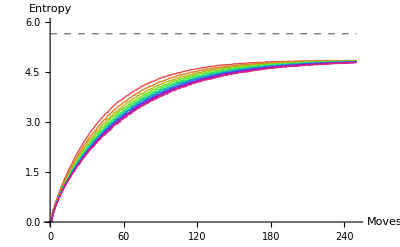

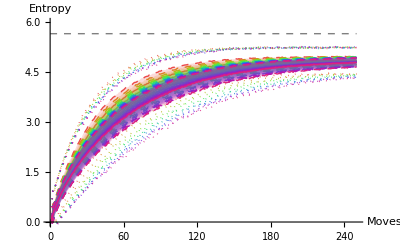

```mathematica
"Pile Shuffle"
rawdata=ReadRawData["pile_shuffle_data.txt"];
plotcount=Length[rawdata]-1;
maxmoves=Length[rawdata[[1]]];

data=rawdata[[2;;,;;]];
Means[data_]:=data[[;;,1]];
Sigmas[data_]:=data[[;;,2]];

colors=Colors[plotcount];
PilePlots[plotconfig_]:=DataPlots[plotconfig,data,colors,{1,maxmoves},2];

Grid[{Range[2,1+Length[colors]],colors},Dividers->Center,FrameStyle->Thin]

limitplot=LimitPlot[maxmoves];

plotconfig={{Means[#]}&,{{#,Thin}}&,{}};
Show[limitplot,PilePlots[plotconfig]]

plotconfig={{Means[#],Means[#]-Sigmas[#],Means[#]+Sigmas[#],Means[#]-sigmamult*Sigmas[#],Means[#]+sigmamult*Sigmas[#]}&,{{#,Thin},{#,Dashed,Thin},{#,Dashed,Thin},{#,Dotted,Thin},{#,Dotted,Thin}}&,{2->{3}}};
Show[limitplot,PilePlots[plotconfig]]
```

Riffle Shuffle

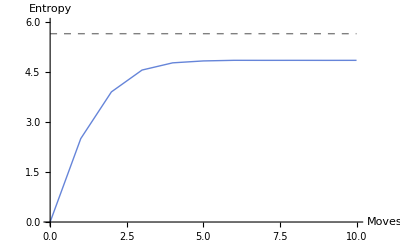

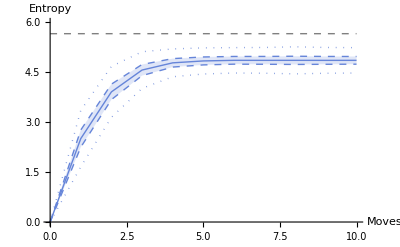

```mathematica
"Riffle Shuffle"
rawdata=ReadRawData["riffle_shuffle_data.txt"];
riffletypes=Length[rawdata];
maxriffles=Length[rawdata[[1]]];

data=rawdata[[;;,;;]];
Means[data_]:=data[[;;,1]];
Sigmas[data_]:=data[[;;,2]];

colors={RGBColor[0.40082222609352647, 0.5220066643438841, 0.85]};
RifflePlots[plotconfig_]:=DataPlots[plotconfig,data,colors,{0,maxriffles-1},1];

limitplot=LimitPlot[maxriffles-1];

plotconfig={{Means[#]}&,{{#,Thin}}&,{}};
Show[limitplot,RifflePlots[plotconfig]]

plotconfig={{Means[#],Means[#]-Sigmas[#],Means[#]+Sigmas[#],Means[#]-sigmamult*Sigmas[#],Means[#]+sigmamult*Sigmas[#]}&,{{#,Thin},{#,Dashed,Thin},{#,Dashed,Thin},{#,Dotted,Thin},{#,Dotted,Thin}}&,{2->{3}}};
Show[limitplot,RifflePlots[plotconfig]]
```

Weave Shuffle

In | Out
RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

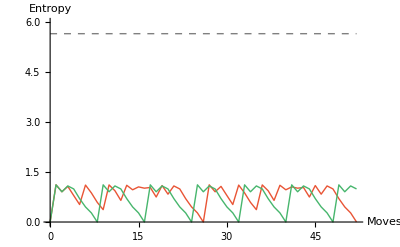

```mathematica
"Weave Shuffle"
rawdata=ReadRawData["weave_shuffle_data.txt"];
weavetypes=Length[rawdata];
maxweaves=Length[rawdata[[1]]];

data=rawdata[[;;,;;]];
Means[data_]:=data[[;;,1]];
Sigmas[data_]:=data[[;;,2]];

colors={RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]};
WeavePlots[plotconfig_]:=DataPlots[plotconfig,data,colors,{0,maxweaves-1},1];

Grid[{{"In","Out"},colors},Dividers->Center,FrameStyle->Thin]

limitplot=LimitPlot[maxweaves-1];
plotconfig={{Means[#]}&,{{#,Thin}}&,{}};
Show[limitplot,WeavePlots[plotconfig]]
```